# Phase-Leistung

## Funktionen

### Includes

```mathematica
<<"Labor.m"
```

## Geräteliste

Oszi:
true rms:
normal:

## 1.) Spitzen und Effektivwerte für verschiedene Kurvenformen

```mathematica
f1= 50;
df1=0;
U1 = 10;
du1=0;
sin={{"Oszi", "true rms", "normal"}, {□, □, □}};
dos=0;
drei={{"Oszi", "true rms", "normal"}, {□, □, □}};
do3=0;
recht={{"Oszi", "true rms", "normal"}, {□, □, □}};
dor=0;
```

## 2.) Phasenlage am Kondensator

Serienschaltung aus R und C. Stelltrafo als Spannungsquelle (U_eff=10V,50Hz).
Spannung an C messen und Strom durch U an R, am Oszi. Damit Phasenverschiebung bestimmen.

```mathematica
f2= 50;
df2=0;
U2 = 10; (*Effektivwert*)
t2=0;
dt2=0;
(*ϕ2=t2*f2*2*π*)
ϕ2=Basic`Fmult[t2,dt2,f2,df2]*2*π
```

{0,0}

## 3.) Wirkleistung in einer RC-Schaltung

### 3.1) 2 Parallele Widerstände

Gleicher Aufbau wie in 2. aber Widerstand durch 2 parallele ersetzen. (Wieviel Ω?)

```mathematica
f31= f2;
df31=0;
U31 = U2; (*Effektivwert*)
du31=0;
```

Spannung an R und C mit "true rms" messen.
Strom messen (ws wieder mit "true rms") und Kapazität berechnen.

```mathematica
Ur31 = 0;

Uc31 =0;
duc31=0;

I31 = 0;
di31=0;

Ca31=(Elec`Fc[I31,du31,Uc31,duc31,f31,df31])/(2*π)
```

Scheinleistung:

```mathematica
PS31=Basic`Fmult[U31,du31,I31,di31];
```

Mit Leistungsmessgerät Wirkleistung messen.

```mathematica
pw31 = 0;
dpw31=0;
```

Phase bestimmen. (ich nehm an mit Oszi)

```mathematica
t31=0;
dt31=0;
ϕ31=Basic`Fmult[t31,dt31,f31,df31]*2*π
```

{0,0}

Z_Ges in Gaußscher Zahlenebene darstellen.

```mathematica
ZG31=Basic`Fdiv[U31,du31,I31,di31];
ListPolarPlot[{{0,0},{ϕ31,ZG31}},Joined-> True]
```

-Graphics-

### 3.2) 3 Parallele Widerstände

Gleicher Aufbau wie in 2. aber Widerstand durch 3 parallele ersetzen. (Wieviel Ω?)

```mathematica
f32= f31;
df32=df31;
U32 = U31; (*Effektivwert*)
du32=du32;
```

Spannung an R und C mit "true rms" messen.
Strom messen (ws wieder mit "true rms") und Kapazität berechnen.

```mathematica
Ur32= 0;

Uc32=0;
duc32=0;

I32 = 0;
di32=0;

Ca32=(Elec`Fc[I32,du32,Uc32,duc32,f32,df32])/(2*π)
```

Scheinleistung:

```mathematica
PS32=Basic`Fmult[U32,du32,I32,di32];
```

Mit Leistungsmessgerät Wirkleistung messen.

```mathematica
pw32 = 0;
dpw32=0;
```

Phase bestimmen. (ich nehm an mit Oszi)

```mathematica
t32=0;
dt32=0;
ϕ32=Basic`Fmult[t32,dt32,f32,df32]*2*π
```

{0,0}

Z_Ges in Gaußscher Zahlenebene darstellen.

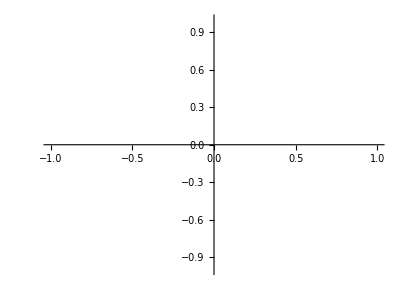

```mathematica
ZG32=Basic`Fdiv[U32,du32,I32,di32];
ListPolarPlot[{{0,0},{ϕ32,ZG32}},Joined-> True]
```